```mathematica
a=1;
a1 = a{1,0};
a2 = a/2{-1,√3};
a3=a/2{-1,-√3};
as={a1,a2,a3};
bs={a2-a3,a3-a1,a1-a2};
```

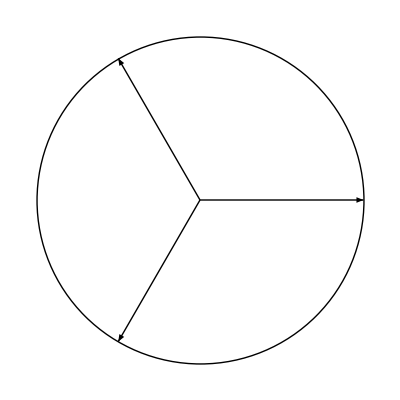

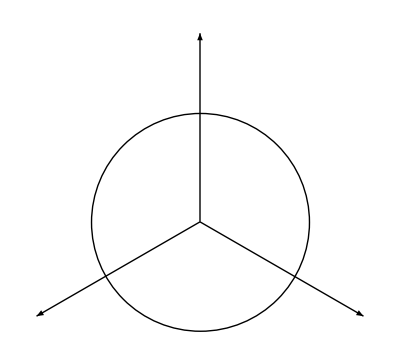

```mathematica
Graphics[{Arrow[{{0,0},#}]&/@as,AspectRatio->1,Axes->True,PlotRange->2{{-1,1},{-1,1}},Circle[]}]
Graphics[{Arrow[{{0,0},#}]&/@bs,AspectRatio->1,Axes->True,PlotRange->3{{-1,1},{-1,1}},Circle[]}]
```

```mathematica
H[k_,as_,bs_]:= t1*Sum[PauliMatrix[1]*Cos[k.a]-PauliMatrix[2]*Sin[k.a],{a,as}] + Sum[v1*Cos[k.a]+v2*Sin[k.a],{a,as}]*PauliMatrix[0] +  t2*Sum[PauliMatrix[3]*Sin[k.b],{b,bs}]+m*PauliMatrix[3]
mass=1;
Manipulate[Plot3D[Evaluate@Eigenvalues[H[{kx,ky},as,bs]/.{t1->1,v1->vd1,v2->vd2,t2->(2mass)/(√3 3),m->mass}],{kx,-π,-0.3π},{ky,-0.8π,0},PlotRange->{-1,1},ViewProjection->"Orthographic",PlotPoints->40,AspectRatio->1,ViewPoint->Top],{{vd1,0},-2,2},{{vd2,0},-2,2}]
```